# Association Rules

## Implementation

```mathematica
(* https://mathematica.stackexchange.com/a/2555 *)
area[r1_,r2_,d_]:=-(1/2)*Sqrt[(d+r1-r2) (d-r1+r2) (-d+r1+r2) (d+r1+r2)]+r1^2 ArcCos[(d^2+r1^2-r2^2)/(2 d r1)]+r2^2 ArcCos[(d^2-r1^2+r2^2)/(2 d r2)];

VennDiagram[area1_?Positive,area2_?Positive,overlap_?NonNegative]/;overlap≤Min[area1,area2]:=Module[{x2,r1=Sqrt[area1/Pi],r2=Sqrt[area2/Pi],d,colors,circles,names},d=Which[overlap==0,r1+r2,overlap==Min[area1,area2],r1-r2,True,Chop[d/.FindRoot[area[r1,r2,d]==overlap,{d,r1}]]];
colors={Pink,Lighter@Lighter@Blue};
circles={{{0,0},r1},{{d,0},r2}};
names={"A","B"};

Graphics[

MapThread[
{
AbsoluteThickness@3,
#1,
Opacity@.3,
Disk@@#2,
Opacity@1,
Circle@@#2,
Style[Text[#3,#2[[1]]],FontFamily->"Libertinus Serif",FontSize->30,FontSlant->Italic]
}&,{colors,circles,names}
],
PlotLabel->"conf(A → B) = "<>ToString[overlap/area1//N]<>"\nconf(B → A) = "<>ToString[overlap/area2//N]
]
];
```

## Part 1: Two Products

We can define the support values as follows:

```mathematica
suppA=1;
suppB=0.5;
suppAB=0.5;
```

and derive the confidence values from here.

```mathematica
confAB=suppAB/suppA
```

0.5

```mathematica
confBA=suppAB/suppB
```

1.

This situation could e.g. correspond to the following Venn diagram.

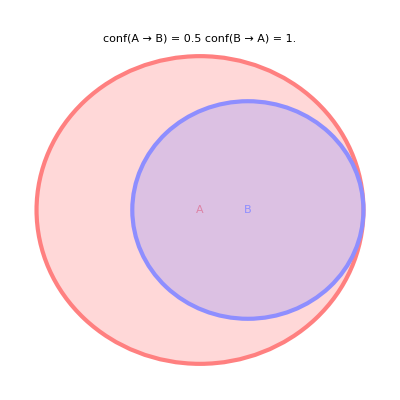

```mathematica
VennDiagram[6,3,3]
```

## Part 2: Set Intersection

The intersection between two singleton item sets with different items is always the empty set. Hence, we always get a support of 0. This is not a useful result.

There is sometimes a confusion why we use support(A∪B) to find out how often two items are used together. This may sound as an intersection problem at first glance. However, the union increases the total item set and this means that less transactions apply to it. Hence, we usually end up with a decreased support value.

## Part 3: Venn Diagram

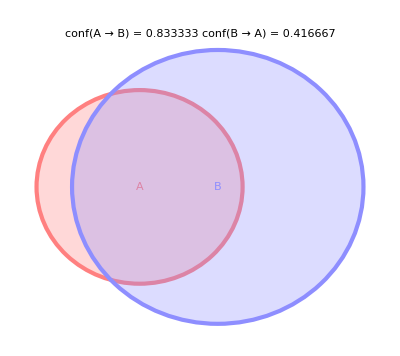
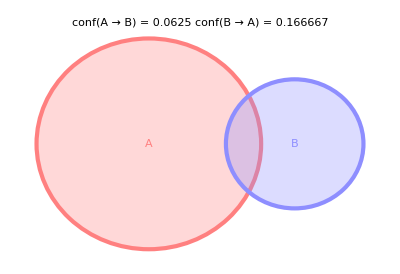
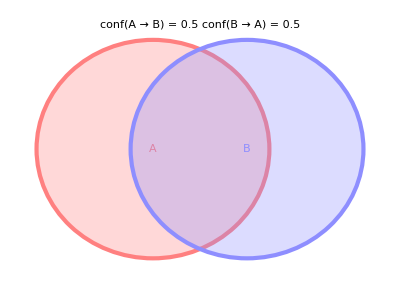
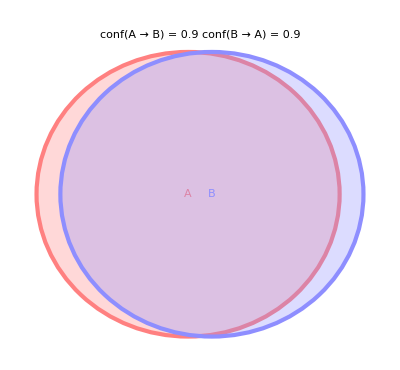

```mathematica
vennDiagrams={
VennDiagram[3,6,2.5],
VennDiagram[8,3,0.5],
VennDiagram[3,3,1.5],
VennDiagram[3,3,2.7]
}
```

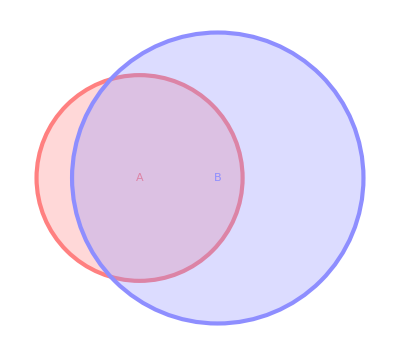
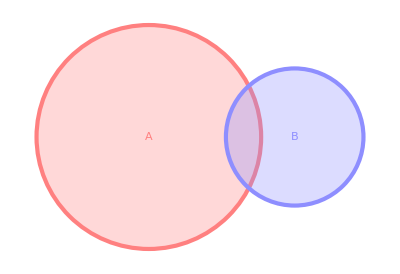
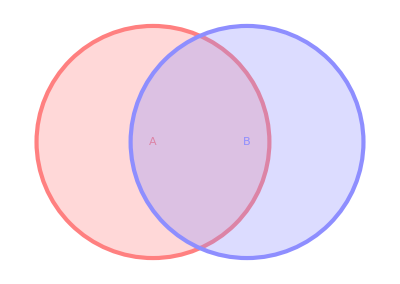
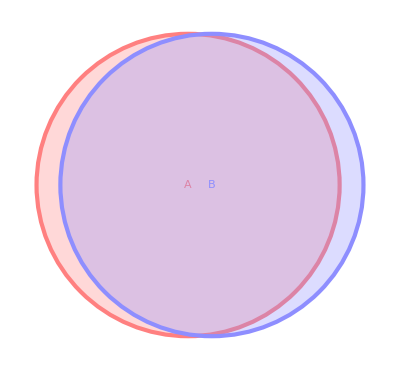

```mathematica
vennDiagramsClean=vennDiagrams/.{(PlotLabel->_)->(PlotLabel->None)}
```

```mathematica
(*Do[
Export[FileNameJoin[{NotebookDirectory[],"VennDiagram"<>ToString[i]<>".pdf"}],vennDiagramsClean[[i]]];
,{i,1,Length[vennDiagramsClean]}]*)
```

## Part 4: Which Support Is Higher?

Starting situation:

conf(A→B)=(support(A∪B))/(support(A))=0.1
conf(B→A)=(support(A∪B))/(support(B))=0.3

We can answer this question logically: support(A) must be higher so that the denominator increases and hence the complete fraction decreases. Alternatively, we can solve the system:

```mathematica
Solve[0.1*A==0.3*B,{A}]
```

{{A→3. B}}